```mathematica
D2[n_,k_,s_]:=D2[n,k,s]=Sum[j^-s D2[Floor[n/j],k-1,s],{j,2,n}];D2[n_,0,s_]:=1
DD[n_,z_,s_]:=Sum[FactorialPower[z,a]/a! D2[n,a,s],{a,0,Log[2,n]}]
```

```mathematica
DD[100,1,0]
```

100

```mathematica
ff[n_] :=Sum[ (DD[j,-1,0]-DD[j-1,-1,0])D[DD[n/j,1,s],s]/.s->0,{j,1,n}]
```

```mathematica
N[ff[100]]
```

-94.0453

```mathematica
ff2[n_] :=Sum[ (DD[j,1,0]-DD[j-1,1,0])D[DD[n/j,-1,s],s]/.s->0,{j,1,n}]
ff2[n_] :=Sum[ D[DD[n/j,-1,s],s]/.s->0,{j,1,n}]
```

```mathematica
N[ff2[100]]
```

94.0453

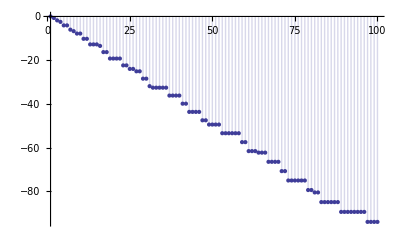

```mathematica
DiscretePlot[ -Sum[ D[DD[n/j,-1,s],s]/.s->0,{j,1,n}],{n,1,100}]
```

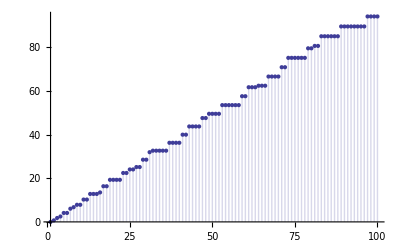

```mathematica
DiscretePlot[ D[Sum[DD[n/j,-1,s],{j,1,n}],{s,1}]/.s->0,{n,1,100}]
```

```mathematica
Sum[ D[DD[3/j,-1,s],{s,1}]/.s->0,{j,1,3}]
```

Log[2]+Log[3]

```mathematica
DiscretePlot[ Sum[ (DD[j,1,0]-DD[j-1,1,0])D[DD[n/j,-1,s],s]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ (D[DD[j,-1,s],s]-D[DD[j-1,-1,s],s])DD[n/j,1,0]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[(1/2) Sum[ (D[DD[j,-2,s],s]-D[DD[j-1,-2,s],s])DD[n/j,2,0]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ (2)(D[DD[j,-1/2,s],s]-D[DD[j-1,-1/2,s],s])DD[n/j,1/2,0]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[  Sum[ 12(D[DD[j,-1/12,s],s]-D[DD[j-1,-1/12,s],s])DD[n/j,1/12,0]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ (1/.0001)(D[DD[j,-.0001,s],s]-D[DD[j-1,-.0001,s],s])DD[n/j,.0001,0]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ Limit[(1/z)(D[DD[j,-z,s],s]-D[DD[j-1,-z,s],s])DD[n/j,z,0]/.s->0,z->0],{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ Limit[(1/z)(DD[j,-z,0]-DD[j-1,-z,0])D[DD[n/j,z,s],s]/.s->0,z->0],{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
N[Limit[D[DD[100,z,s],s]/z /.s->0,z->0]]
```

-94.0453

```mathematica
DiscretePlot[ Sum[ Limit[(1/z)(D[DD[j,-z,s],s]-D[DD[j-1,-z,s],s])/.s->0,z->0],{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[ Sum[ D[DD[n/j,-1,s],{s,1}]/.s->0,{j,1,n}],{n,1,100}]
```

-Graphics-

```mathematica
Sum[ Limit[D[DD[100/j,z,0],{z,1}],z->-1],{j,1,100}]
```

428/15

```mathematica
N[Sum[ Limit[D[DD[100/j,z,s],s]/.s->0,z->-1],{j,1,100}]]
```

94.0453

```mathematica
N[ Limit[D[DD[100,z,s],z]/.s->0,z->0]]
```

28.5333